```mathematica
Conversion[(RightArrow | Rule | LongRightArrow)[A__,B__]] := Conversion/@{A,"->",B};
Conversion[(Equilibrium|ReverseEquilibrium|LeftRightArrow|LongLeftRightArrow| RightArrowLeftArrow| LeftArrowRightArrow)[A_,B__]] :=
Conversion/@{A,"⇌",Conversion[B]};
Conversion[(LeftArrow | LongLeftArrow)[A_,B_]] := Conversion/@{A,"<-",B};
Conversion[Sequence[A__]] := Riffle[List[A],"⇌"];

NotListQ[l_] := Head[l]=!=List;

SimplifyReactions[Reactions___] := 
Block[{$RecursionLimit = 10^3},
DeleteDuplicates[Flatten[
(Partition[#,3,2]&/@(Flatten[Conversion[#]]&/@{Reactions}))/.{{A_,"->",B_}->{{A,B}},{A_,"⇌",B_}-> {{A,B},{B,A}},{A_,"<-",B_}->{{B,A}}},2]]/.{A_?NotListQ, A_?NotListQ}->Sequence[]];

ReactionsData[Reactions___,ExternalSpecs_List:{}] := 
Module[{s=SimplifyReactions[Reactions],sp,ab,gamma,fhj,cpx,deficiency,var,kcoef,detmodel},
sp = Complement[Variables[(s/.r_*A_?StringQ ->A)//.(A_+B_)->{A,B}],Join[ExternalSpecs,{"0"}]];
Echo[sp];
{ab,fhj,cpx}= {Transpose/@ Transpose[Outer[Coefficient,s,sp]],s/.{A_?NotListQ,B_?NotListQ}->RightArrow[A,B],Union[Flatten[s]/.Thread[ExternalSpecs->0]]};
gamma=First[Differences[ab]];
{var,kcoef}={#[Symbol["t"]] &/@ (Subscript[Symbol["c"], #] & /@ sp),Array[Subscript[Symbol["k"], #]&, Length[ab[[1,1]]]]};
Echo[var];
Echo[# &/@ (Subscript[Symbol["c"], #] & /@ sp)];
Echo[#[0]==0 &/@ (Subscript[Symbol["c"], #] & /@ sp)];
Echo[kcoef];
detmodel=Thread[D[var,t] == gamma.(kcoef (Inner[Power,var,#,Times]&/@Transpose[First[ab]]))];
Echo[detmodel];
{fhj,Length[fhj],sp,Length[sp],ExternalSpecs,Length[ExternalSpecs],cpx,Length[cpx],Part[ab,1],Part[ab,2],gamma, Column[detmodel]}];

DescriptiveRK[l_List]:=
Module[{reac=ReactionsData@@l,h},
h=Part[reac,{4,2}];
Grid[MapThread[{#1,If[NumberQ[#2],#2,If[MatrixQ[#2],#2//MatrixForm,#2]]}&,{Data,reac}],Dividers->Center,FrameStyle->Directive[Brown],Spacings->{1,1.5},Alignment->{{Right,Left},Center},ItemStyle->{{Directive[Blue,13,Bold],Directive[Black,13,Bold]}},Background->{{Lighter[Yellow,.8],Lighter[Orange,.8]}}]];

Data={"complex chemical reaction","number of reaction steps","chemical species","number of chemical species","external species","number of external species","complexes","number of complexes",Column[{"matrix of reactant" ,"complex vectors (α)"},Right],Column[{"matrix of product","complex vectors (β)"},Right],"stoichiometric matrix (γ)",Column[{"induced mass action kinetic","differential equations","(CCD model)"},Right]};

Models = {"A + B → C","A + B ⇄ C","autocatalator","Belousov–Zhabotinsky",
"Brusselator","Eigen", "explodator","Feinberg–Horn I","Feinberg–Horn II","irreversible triangle reaction","reversible triangle reaction","Hudson–Rössler","Ivanova","Leonard–Reichl","Michaelis–Menten",
"Oregonator","Schlögl","Verhulst","Volterra–Lotka"};

BuiltInReactions =
Thread[Models->{
{A+B->C},{A+B⇄C},{A->X,X->Y,X+2Y->3Y,Y->P,{A,P}},
{X+Y+H->2W,Y+A+2H->X+W,2X->W,X+2A+2H->2X+2Z,2X+2Z->X,Z+O->Q,Z+W->Y,W->Y,{H,A,O,Q}},
{X←A,B+X->Y+D,Y+2X->3X,X->W,{A,B,D,W}},
{X->0,X->2X},{A+X->2X,X+Y-> Z,Z->2Y,Y->P,{A,P}},
{3X-> 2X+2Y-> 3Y-> 2X+Y-> 3X},{X⇌Y,X+Z-> T-> Y+ U->X+Z},
{C->A-> B->C},{A⇋B↔"C"⇄A},{P-> A,Q-> B,A+B->2B,B-> R,A↔C,{P,Q,R}},
{X+Y-> 2Y,Y+Z->2Z,X+Z->2Y},{2X⇆Y},
{"E"+S⇌C->"E"+P},{A+Y->X,X+Y->P,B+X->2X+Z,2X->Q,{A,P,B,Q}},{0⇌X,2X⇌3X},{X⇌2X},{X+A-> 2X,X+Y-> 2Y,B←Y,{A,B}}}];
```

```mathematica
(*cas13 pre-equilibration*)
```

```mathematica
(*rates of stuff*)
cas13Binding = 1;
cas13DissocGuide = 5;
cas13DissocSubs = 2000;
cas13DissocTarget = 1;
cas13Clevage = 200;
cas13Background = cas13Clevage/(5*10^8);
csm6ActivatorBinding = 1;
csm6ActivatorUnbinding = 63; (*Km from tina turn into kd at some point*)
csm6ActivatorCleavage = 0;
csm6Kcat = 0.4;
csm6SubstrateBinding = 1;
csm6SubstrateUnbinding = 5000;(*Kd? from tina turn maybe its a Km*)
csm6SubstrateUnbinding
```

5000

```mathematica
(*concentrations*)
reporterInitial = 200;
cas13Initial = 50;
guideInitial = 50;
rnpInitial = 0;
a4u6Initial = 2000;
csm6Initial = 100;
csm6Initial
```

100

```mathematica
rnpProduction = {{cas13 + guide ⇌ rnp, {cas13Binding, cas13DissocGuide}}};
Dimensions[rnpProduction]
eqs = rnpProduction[[All,1]]
DescriptiveRK[eqs]
rates = Flatten[rnpProduction[[All,2]]]
```

{1,2}

{cas13+guide⇌rnp}

{cas13,guide,rnp}

{c_cas13[t],c_guide[t],c_rnp[t]}

{c_cas13,c_guide,c_rnp}

{c_cas13[0]==0,c_guide[0]==0,c_rnp[0]==0}

{k_1,k_2}

{c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]}

complex chemical reaction | {cas13+guide→rnp,rnp→cas13+guide}
number of reaction steps | 2
chemical species | {cas13,guide,rnp}
number of chemical species | 3
external species | {}
number of external species | 0
complexes | {cas13+guide,rnp}
number of complexes | 2
matrix of reactant
complex vectors (α) | (1 | 0
1 | 0
0 | 1)
matrix of product
complex vectors (β) | (0 | 1
0 | 1
1 | 0)
stoichiometric matrix (γ) | (-1 | 1
-1 | 1
1 | -1)
induced mass action kinetic
differential equations
(CCD model) | c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]

{1,5}

```mathematica
diffEqs = {Subscript[c, cas13]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, guide]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, rnp]'[t]==Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]-Subscript[k, 2] Subscript[c, rnp][t]}/.Thread[{Subscript[k, 1],Subscript[k, 2]} -> rates]
```

{c_cas13'[t]==-c_cas13[t] c_guide[t]+5 c_rnp[t],c_guide'[t]==-c_cas13[t] c_guide[t]+5 c_rnp[t],c_rnp'[t]==c_cas13[t] c_guide[t]-5 c_rnp[t]}

```mathematica
initialConds = {Subscript[c, cas13][0]==cas13Initial,Subscript[c, guide][0]== guideInitial,Subscript[c, rnp][0]==0}
toSolve= Join[diffEqs,initialConds]
solved = NDSolve[toSolve, {Subscript[c, cas13],Subscript[c, guide],Subscript[c, rnp]},{t, 0, 2000},MaxStepSize -> 0.001]
```

{c_cas13[0]==50,c_guide[0]==50,c_rnp[0]==0}

{c_cas13'[t]==-c_cas13[t] c_guide[t]+5 c_rnp[t],c_guide'[t]==-c_cas13[t] c_guide[t]+5 c_rnp[t],c_rnp'[t]==c_cas13[t] c_guide[t]-5 c_rnp[t],c_cas13[0]==50,c_guide[0]==50,c_rnp[0]==0}

{{c_cas13→InterpolatingFunction[{{0., 2000.}}, <>],c_guide→InterpolatingFunction[{{0., 2000.}}, <>],c_rnp→InterpolatingFunction[{{0., 2000.}}, <>]}}

```mathematica
rnpf = Subscript[c, rnp]/.First@solved
cas13f = Subscript[c, cas13]/.First@solved
guidef = Subscript[c, guide]/.First@solved
```

InterpolatingFunction[{{0., 2000.}}, <>]

InterpolatingFunction[{{0., 2000.}}, <>]

InterpolatingFunction[{{0., 2000.}}, <>]

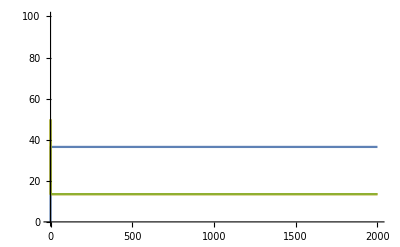

```mathematica
Plot[{rnpf[t],cas13f[t], guidef[t]},{t, 0, 2000},PlotRange->{0,100}]
```

```mathematica
rnpf[2000]
cas13f[2000]
guidef[2000]
```

36.4922

13.5078

13.5078

```mathematica
(*cas13 alone*)
```

```mathematica
(*concentrations*)
reporterInitial = 200;
cas13Initial = 13.507810593582104;
guideInitial = 13.507810593582104;
rnpInitial = 36.49218940641761;
a4u6Initial = 2000;
csm6Initial = 100;
csm6Initial
(*PlotLegends->LineLegend[Flatten[Table["Viral Load: "<>ToString[b],Evaluate@viralSweep], 1],LegendLabel->x]*)
```

100

```mathematica
(*csm6 secondary*)
csm6ActivatorCleavage=0;
onTargetCas13 = {{cas13 + guide ⇌ rnp, {cas13Binding, cas13DissocTarget}},
{rnp + target ⇌ rnpActive, {cas13Binding, cas13DissocTarget}},
{rnpActive + a4u6 ⇌ rnpActivea4u6, {cas13Binding, cas13DissocSubs}},
{rnpActivea4u6 -> rnpActive + a4, {cas13Clevage}}
};
backgroundCas13 = {{rnp +a4u6 ⇌ rnpa4u6, {cas13Binding, cas13DissocSubs}},
{rnpa4u6 -> rnp + a4, {cas13Background}}
};
csm6Reactions = {{csm6 + a4 ⇌ csm6Active, {csm6ActivatorBinding, csm6ActivatorUnbinding-csm6ActivatorCleavage}},
{csm6Active -> csm6, {csm6ActivatorCleavage}},
{csm6Active + reporter ⇌ csm6ActiveReporter, {csm6SubstrateBinding, csm6SubstrateUnbinding}},
{csm6ActiveReporter -> csm6Active +product, {csm6Kcat}}
};

rxns = Join[onTargetCas13, backgroundCas13, csm6Reactions]
Dimensions[rxns]
eqs = rxns[[All,1]]
DescriptiveRK[eqs]
rates = Flatten[rxns[[All,2]]]
```

{{cas13+guide⇌rnp,{1,1}},{rnp+target⇌rnpActive,{1,1}},{a4u6+rnpActive⇌rnpActivea4u6,{1,2000}},{rnpActivea4u6→a4+rnpActive,{200}},{a4u6+rnp⇌rnpa4u6,{1,2000}},{rnpa4u6→a4+rnp,{1/2500000}},{a4+csm6⇌csm6Active,{1,63}},{csm6Active→csm6,{0}},{csm6Active+reporter⇌csm6ActiveReporter,{1,5000}},{csm6ActiveReporter→csm6Active+product,{0.4}}}

{10,2}

{cas13+guide⇌rnp,rnp+target⇌rnpActive,a4u6+rnpActive⇌rnpActivea4u6,rnpActivea4u6→a4+rnpActive,a4u6+rnp⇌rnpa4u6,rnpa4u6→a4+rnp,a4+csm6⇌csm6Active,csm6Active→csm6,csm6Active+reporter⇌csm6ActiveReporter,csm6ActiveReporter→csm6Active+product}

{a4,a4u6,cas13,csm6,csm6Active,csm6ActiveReporter,guide,product,reporter,rnp,rnpa4u6,rnpActive,rnpActivea4u6,target}

{c_a4[t],c_a4u6[t],c_cas13[t],c_csm6[t],c_csm6Active[t],c_csm6ActiveReporter[t],c_guide[t],c_product[t],c_reporter[t],c_rnp[t],c_rnpa4u6[t],c_rnpActive[t],c_rnpActivea4u6[t],c_target[t]}

{c_a4,c_a4u6,c_cas13,c_csm6,c_csm6Active,c_csm6ActiveReporter,c_guide,c_product,c_reporter,c_rnp,c_rnpa4u6,c_rnpActive,c_rnpActivea4u6,c_target}

{c_a4[0]==0,c_a4u6[0]==0,c_cas13[0]==0,c_csm6[0]==0,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==0,c_product[0]==0,c_reporter[0]==0,c_rnp[0]==0,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==0}

{k_1,k_2,k_3,k_4,k_5,k_6,k_7,k_8,k_9,k_10,k_11,k_12,k_13,k_14,k_15,k_16}

{c_a4'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_10 c_rnpa4u6[t]+k_7 c_rnpActivea4u6[t],c_a4u6'[t]==-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t],c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_csm6'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_13 c_csm6Active[t],c_csm6Active'[t]==k_11 c_a4[t] c_csm6[t]-k_12 c_csm6Active[t]-k_13 c_csm6Active[t]+k_15 c_csm6ActiveReporter[t]+k_16 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-k_15 c_csm6ActiveReporter[t]-k_16 c_csm6ActiveReporter[t]+k_14 c_csm6Active[t] c_reporter[t],c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_product'[t]==k_16 c_csm6ActiveReporter[t],c_reporter'[t]==k_15 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t],c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]+k_10 c_rnpa4u6[t]+k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t],c_rnpa4u6'[t]==k_8 c_a4u6[t] c_rnp[t]-k_9 c_rnpa4u6[t]-k_10 c_rnpa4u6[t],c_rnpActive'[t]==-k_4 c_rnpActive[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]+k_7 c_rnpActivea4u6[t]+k_3 c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==k_5 c_a4u6[t] c_rnpActive[t]-k_6 c_rnpActivea4u6[t]-k_7 c_rnpActivea4u6[t],c_target'[t]==k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]}

complex chemical reaction | {cas13+guide→rnp,rnp→cas13+guide,rnp+target→rnpActive,rnpActive→rnp+target,a4u6+rnpActive→rnpActivea4u6,rnpActivea4u6→a4u6+rnpActive,rnpActivea4u6→a4+rnpActive,a4u6+rnp→rnpa4u6,rnpa4u6→a4u6+rnp,rnpa4u6→a4+rnp,a4+csm6→csm6Active,csm6Active→a4+csm6,csm6Active→csm6,csm6Active+reporter→csm6ActiveReporter,csm6ActiveReporter→csm6Active+reporter,csm6ActiveReporter→csm6Active+product}
number of reaction steps | 16
chemical species | {a4,a4u6,cas13,csm6,csm6Active,csm6ActiveReporter,guide,product,reporter,rnp,rnpa4u6,rnpActive,rnpActivea4u6,target}
number of chemical species | 14
external species | {}
number of external species | 0
complexes | {csm6,a4+csm6,csm6Active,csm6ActiveReporter,cas13+guide,csm6Active+product,csm6Active+reporter,rnp,a4+rnp,a4u6+rnp,rnpa4u6,rnpActive,a4+rnpActive,a4u6+rnpActive,rnpActivea4u6,rnp+target}
number of complexes | 16
matrix of reactant
complex vectors (α) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
matrix of product
complex vectors (β) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
stoichiometric matrix (γ) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0
1 | -1 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
induced mass action kinetic
differential equations
(CCD model) | c_a4'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_10 c_rnpa4u6[t]+k_7 c_rnpActivea4u6[t]
c_a4u6'[t]==-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]
c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_csm6'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_13 c_csm6Active[t]
c_csm6Active'[t]==k_11 c_a4[t] c_csm6[t]-k_12 c_csm6Active[t]-k_13 c_csm6Active[t]+k_15 c_csm6ActiveReporter[t]+k_16 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t]
c_csm6ActiveReporter'[t]==-k_15 c_csm6ActiveReporter[t]-k_16 c_csm6ActiveReporter[t]+k_14 c_csm6Active[t] c_reporter[t]
c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_product'[t]==k_16 c_csm6ActiveReporter[t]
c_reporter'[t]==k_15 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t]
c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]+k_10 c_rnpa4u6[t]+k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]
c_rnpa4u6'[t]==k_8 c_a4u6[t] c_rnp[t]-k_9 c_rnpa4u6[t]-k_10 c_rnpa4u6[t]
c_rnpActive'[t]==-k_4 c_rnpActive[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]+k_7 c_rnpActivea4u6[t]+k_3 c_rnp[t] c_target[t]
c_rnpActivea4u6'[t]==k_5 c_a4u6[t] c_rnpActive[t]-k_6 c_rnpActivea4u6[t]-k_7 c_rnpActivea4u6[t]
c_target'[t]==k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]

{1,1,1,1,1,2000,200,1,2000,1/2500000,1,63,0,1,5000,0.4}

```mathematica
diffEqs = {Subscript[c, a4]'[t]==-Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]+Subscript[k, 12] Subscript[c, csm6Active][t]+Subscript[k, 10] Subscript[c, rnpa4u6][t]+Subscript[k, 7] Subscript[c, rnpActivea4u6][t],Subscript[c, a4u6]'[t]==-Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]+Subscript[k, 9] Subscript[c, rnpa4u6][t]-Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]+Subscript[k, 6] Subscript[c, rnpActivea4u6][t],Subscript[c, cas13]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, csm6]'[t]==-Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]+Subscript[k, 12] Subscript[c, csm6Active][t]+Subscript[k, 13] Subscript[c, csm6Active][t],Subscript[c, csm6Active]'[t]==Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]-Subscript[k, 12] Subscript[c, csm6Active][t]-Subscript[k, 13] Subscript[c, csm6Active][t]+Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]+Subscript[k, 16] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, csm6ActiveReporter]'[t]==-Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 16] Subscript[c, csm6ActiveReporter][t]+Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, guide]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, product]'[t]==Subscript[k, 16] Subscript[c, csm6ActiveReporter][t],Subscript[c, reporter]'[t]==Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, rnp]'[t]==Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]-Subscript[k, 2] Subscript[c, rnp][t]-Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]+Subscript[k, 9] Subscript[c, rnpa4u6][t]+Subscript[k, 10] Subscript[c, rnpa4u6][t]+Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t],Subscript[c, rnpa4u6]'[t]==Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]-Subscript[k, 9] Subscript[c, rnpa4u6][t]-Subscript[k, 10] Subscript[c, rnpa4u6][t],Subscript[c, rnpActive]'[t]==-Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]+Subscript[k, 6] Subscript[c, rnpActivea4u6][t]+Subscript[k, 7] Subscript[c, rnpActivea4u6][t]+Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t],Subscript[c, rnpActivea4u6]'[t]==Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]-Subscript[k, 6] Subscript[c, rnpActivea4u6][t]-Subscript[k, 7] Subscript[c, rnpActivea4u6][t],Subscript[c, target]'[t]==Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t]}/.Thread[{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6],Subscript[k, 7],Subscript[k, 8],Subscript[k, 9],Subscript[k, 10],Subscript[k, 11],Subscript[k, 12],Subscript[k, 13],Subscript[k, 14],Subscript[k, 15],Subscript[k, 16]} -> rates]
initialConds = {Subscript[c, a4][0]==0,Subscript[c, a4u6][0]==a4u6Initial,Subscript[c, cas13][0]==cas13Initial,Subscript[c, csm6][0]==csm6Initial,Subscript[c, csm6Active][0]==0,Subscript[c, csm6ActiveReporter][0]==0,Subscript[c, guide][0]==guideInitial,Subscript[c, product][0]==0,Subscript[c, reporter][0]==reporterInitial,Subscript[c, rnp][0]==rnpInitial,Subscript[c, rnpa4u6][0]==0,Subscript[c, rnpActive][0]==0,Subscript[c, rnpActivea4u6][0]==0,Subscript[c, target][0]==targetInitial}
toSolve= Join[diffEqs,initialConds]
```

{c_a4'[t]==-c_a4[t] c_csm6[t]+63 c_csm6Active[t]+c_rnpa4u6[t]/2500000+200 c_rnpActivea4u6[t],c_a4u6'[t]==-c_a4u6[t] c_rnp[t]+2000 c_rnpa4u6[t]-c_a4u6[t] c_rnpActive[t]+2000 c_rnpActivea4u6[t],c_cas13'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_csm6'[t]==-c_a4[t] c_csm6[t]+63 c_csm6Active[t],c_csm6Active'[t]==c_a4[t] c_csm6[t]-63 c_csm6Active[t]+5000.4 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-5000.4 c_csm6ActiveReporter[t]+c_csm6Active[t] c_reporter[t],c_guide'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_product'[t]==0.4 c_csm6ActiveReporter[t],c_reporter'[t]==5000 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_rnp'[t]==c_cas13[t] c_guide[t]-c_rnp[t]-c_a4u6[t] c_rnp[t]+(5000000001 c_rnpa4u6[t])/2500000+c_rnpActive[t]-c_rnp[t] c_target[t],c_rnpa4u6'[t]==c_a4u6[t] c_rnp[t]-(5000000001 c_rnpa4u6[t])/2500000,c_rnpActive'[t]==-c_rnpActive[t]-c_a4u6[t] c_rnpActive[t]+2200 c_rnpActivea4u6[t]+c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==c_a4u6[t] c_rnpActive[t]-2200 c_rnpActivea4u6[t],c_target'[t]==c_rnpActive[t]-c_rnp[t] c_target[t]}

{c_a4[0]==0,c_a4u6[0]==2000,c_cas13[0]==13.5078,c_csm6[0]==100,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==13.5078,c_product[0]==0,c_reporter[0]==200,c_rnp[0]==36.4922,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==targetInitial}

{c_a4'[t]==-c_a4[t] c_csm6[t]+63 c_csm6Active[t]+c_rnpa4u6[t]/2500000+200 c_rnpActivea4u6[t],c_a4u6'[t]==-c_a4u6[t] c_rnp[t]+2000 c_rnpa4u6[t]-c_a4u6[t] c_rnpActive[t]+2000 c_rnpActivea4u6[t],c_cas13'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_csm6'[t]==-c_a4[t] c_csm6[t]+63 c_csm6Active[t],c_csm6Active'[t]==c_a4[t] c_csm6[t]-63 c_csm6Active[t]+5000.4 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-5000.4 c_csm6ActiveReporter[t]+c_csm6Active[t] c_reporter[t],c_guide'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_product'[t]==0.4 c_csm6ActiveReporter[t],c_reporter'[t]==5000 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_rnp'[t]==c_cas13[t] c_guide[t]-c_rnp[t]-c_a4u6[t] c_rnp[t]+(5000000001 c_rnpa4u6[t])/2500000+c_rnpActive[t]-c_rnp[t] c_target[t],c_rnpa4u6'[t]==c_a4u6[t] c_rnp[t]-(5000000001 c_rnpa4u6[t])/2500000,c_rnpActive'[t]==-c_rnpActive[t]-c_a4u6[t] c_rnpActive[t]+2200 c_rnpActivea4u6[t]+c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==c_a4u6[t] c_rnpActive[t]-2200 c_rnpActivea4u6[t],c_target'[t]==c_rnpActive[t]-c_rnp[t] c_target[t],c_a4[0]==0,c_a4u6[0]==2000,c_cas13[0]==13.5078,c_csm6[0]==100,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==13.5078,c_product[0]==0,c_reporter[0]==200,c_rnp[0]==36.4922,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==targetInitial}

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

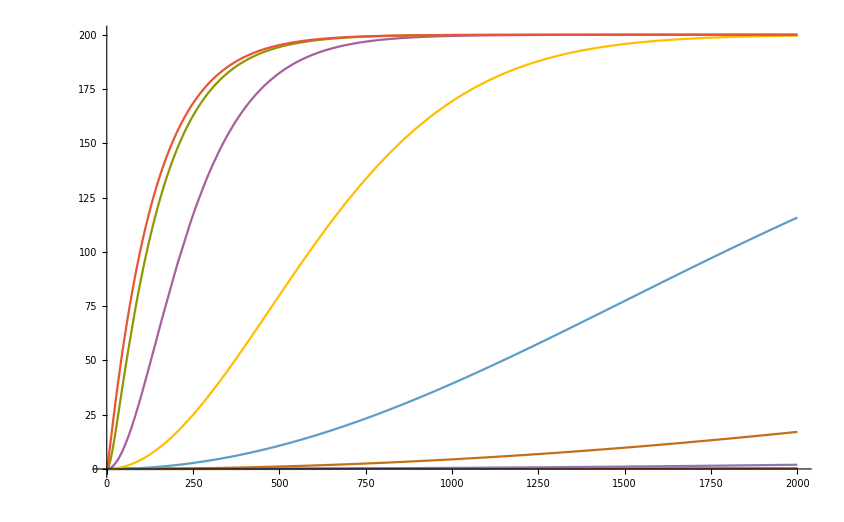

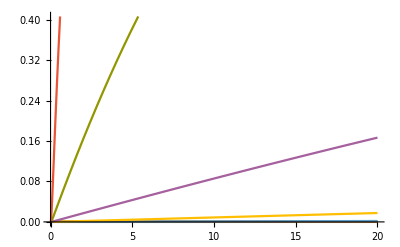

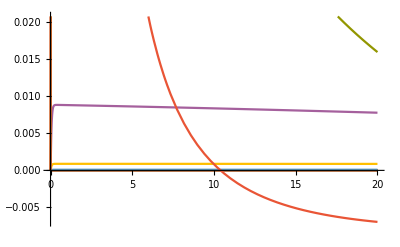

```mathematica
getProduct[viralLoad_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial} -> {viralLoad}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
```

```mathematica
(*csm6 secondary activator cleavage*)
csm6ActivatorCleavage= cleavageRate;
onTargetCas13 = {{cas13 + guide ⇌ rnp, {cas13Binding, cas13DissocTarget}},
{rnp + target ⇌ rnpActive, {cas13Binding, cas13DissocTarget}},
{rnpActive + a4u6 ⇌ rnpActivea4u6, {cas13Binding, cas13DissocSubs}},
{rnpActivea4u6 -> rnpActive + a4, {cas13Clevage}}
};
backgroundCas13 = {{rnp +a4u6 ⇌ rnpa4u6, {cas13Binding, cas13DissocSubs}},
{rnpa4u6 -> rnp + a4, {cas13Background}}
};
csm6Reactions = {{csm6 + a4 ⇌ csm6Active, {csm6ActivatorBinding, csm6ActivatorUnbinding-csm6ActivatorCleavage}},
{csm6Active -> csm6, {csm6ActivatorCleavage}},
{csm6Active + reporter ⇌ csm6ActiveReporter, {csm6SubstrateBinding, csm6SubstrateUnbinding}},
{csm6ActiveReporter -> csm6Active +product, {csm6Kcat}}
};

rxns = Join[onTargetCas13, backgroundCas13, csm6Reactions]
Dimensions[rxns]
eqs = rxns[[All,1]]
DescriptiveRK[eqs]
rates = Flatten[rxns[[All,2]]]
```

{{cas13+guide⇌rnp,{1,1}},{rnp+target⇌rnpActive,{1,1}},{a4u6+rnpActive⇌rnpActivea4u6,{1,2000}},{rnpActivea4u6→a4+rnpActive,{200}},{a4u6+rnp⇌rnpa4u6,{1,2000}},{rnpa4u6→a4+rnp,{1/2500000}},{a4+csm6⇌csm6Active,{1,63-cleavageRate}},{csm6Active→csm6,{cleavageRate}},{csm6Active+reporter⇌csm6ActiveReporter,{1,5000}},{csm6ActiveReporter→csm6Active+product,{0.4}}}

{10,2}

{cas13+guide⇌rnp,rnp+target⇌rnpActive,a4u6+rnpActive⇌rnpActivea4u6,rnpActivea4u6→a4+rnpActive,a4u6+rnp⇌rnpa4u6,rnpa4u6→a4+rnp,a4+csm6⇌csm6Active,csm6Active→csm6,csm6Active+reporter⇌csm6ActiveReporter,csm6ActiveReporter→csm6Active+product}

{a4,a4u6,cas13,csm6,csm6Active,csm6ActiveReporter,guide,product,reporter,rnp,rnpa4u6,rnpActive,rnpActivea4u6,target}

{c_a4[t],c_a4u6[t],c_cas13[t],c_csm6[t],c_csm6Active[t],c_csm6ActiveReporter[t],c_guide[t],c_product[t],c_reporter[t],c_rnp[t],c_rnpa4u6[t],c_rnpActive[t],c_rnpActivea4u6[t],c_target[t]}

{c_a4,c_a4u6,c_cas13,c_csm6,c_csm6Active,c_csm6ActiveReporter,c_guide,c_product,c_reporter,c_rnp,c_rnpa4u6,c_rnpActive,c_rnpActivea4u6,c_target}

{c_a4[0]==0,c_a4u6[0]==0,c_cas13[0]==0,c_csm6[0]==0,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==0,c_product[0]==0,c_reporter[0]==0,c_rnp[0]==0,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==0}

{k_1,k_2,k_3,k_4,k_5,k_6,k_7,k_8,k_9,k_10,k_11,k_12,k_13,k_14,k_15,k_16}

{c_a4'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_10 c_rnpa4u6[t]+k_7 c_rnpActivea4u6[t],c_a4u6'[t]==-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t],c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_csm6'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_13 c_csm6Active[t],c_csm6Active'[t]==k_11 c_a4[t] c_csm6[t]-k_12 c_csm6Active[t]-k_13 c_csm6Active[t]+k_15 c_csm6ActiveReporter[t]+k_16 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-k_15 c_csm6ActiveReporter[t]-k_16 c_csm6ActiveReporter[t]+k_14 c_csm6Active[t] c_reporter[t],c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_product'[t]==k_16 c_csm6ActiveReporter[t],c_reporter'[t]==k_15 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t],c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]+k_10 c_rnpa4u6[t]+k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t],c_rnpa4u6'[t]==k_8 c_a4u6[t] c_rnp[t]-k_9 c_rnpa4u6[t]-k_10 c_rnpa4u6[t],c_rnpActive'[t]==-k_4 c_rnpActive[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]+k_7 c_rnpActivea4u6[t]+k_3 c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==k_5 c_a4u6[t] c_rnpActive[t]-k_6 c_rnpActivea4u6[t]-k_7 c_rnpActivea4u6[t],c_target'[t]==k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]}

complex chemical reaction | {cas13+guide→rnp,rnp→cas13+guide,rnp+target→rnpActive,rnpActive→rnp+target,a4u6+rnpActive→rnpActivea4u6,rnpActivea4u6→a4u6+rnpActive,rnpActivea4u6→a4+rnpActive,a4u6+rnp→rnpa4u6,rnpa4u6→a4u6+rnp,rnpa4u6→a4+rnp,a4+csm6→csm6Active,csm6Active→a4+csm6,csm6Active→csm6,csm6Active+reporter→csm6ActiveReporter,csm6ActiveReporter→csm6Active+reporter,csm6ActiveReporter→csm6Active+product}
number of reaction steps | 16
chemical species | {a4,a4u6,cas13,csm6,csm6Active,csm6ActiveReporter,guide,product,reporter,rnp,rnpa4u6,rnpActive,rnpActivea4u6,target}
number of chemical species | 14
external species | {}
number of external species | 0
complexes | {csm6,a4+csm6,csm6Active,csm6ActiveReporter,cas13+guide,csm6Active+product,csm6Active+reporter,rnp,a4+rnp,a4u6+rnp,rnpa4u6,rnpActive,a4+rnpActive,a4u6+rnpActive,rnpActivea4u6,rnp+target}
number of complexes | 16
matrix of reactant
complex vectors (α) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
matrix of product
complex vectors (β) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
stoichiometric matrix (γ) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0
1 | -1 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
induced mass action kinetic
differential equations
(CCD model) | c_a4'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_10 c_rnpa4u6[t]+k_7 c_rnpActivea4u6[t]
c_a4u6'[t]==-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]
c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_csm6'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_13 c_csm6Active[t]
c_csm6Active'[t]==k_11 c_a4[t] c_csm6[t]-k_12 c_csm6Active[t]-k_13 c_csm6Active[t]+k_15 c_csm6ActiveReporter[t]+k_16 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t]
c_csm6ActiveReporter'[t]==-k_15 c_csm6ActiveReporter[t]-k_16 c_csm6ActiveReporter[t]+k_14 c_csm6Active[t] c_reporter[t]
c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_product'[t]==k_16 c_csm6ActiveReporter[t]
c_reporter'[t]==k_15 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t]
c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]+k_10 c_rnpa4u6[t]+k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]
c_rnpa4u6'[t]==k_8 c_a4u6[t] c_rnp[t]-k_9 c_rnpa4u6[t]-k_10 c_rnpa4u6[t]
c_rnpActive'[t]==-k_4 c_rnpActive[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]+k_7 c_rnpActivea4u6[t]+k_3 c_rnp[t] c_target[t]
c_rnpActivea4u6'[t]==k_5 c_a4u6[t] c_rnpActive[t]-k_6 c_rnpActivea4u6[t]-k_7 c_rnpActivea4u6[t]
c_target'[t]==k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]

{1,1,1,1,1,2000,200,1,2000,1/2500000,1,63-cleavageRate,cleavageRate,1,5000,0.4}

```mathematica
diffEqs = {Subscript[c, a4]'[t]==-Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]+Subscript[k, 12] Subscript[c, csm6Active][t]+Subscript[k, 10] Subscript[c, rnpa4u6][t]+Subscript[k, 7] Subscript[c, rnpActivea4u6][t],Subscript[c, a4u6]'[t]==-Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]+Subscript[k, 9] Subscript[c, rnpa4u6][t]-Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]+Subscript[k, 6] Subscript[c, rnpActivea4u6][t],Subscript[c, cas13]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, csm6]'[t]==-Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]+Subscript[k, 12] Subscript[c, csm6Active][t]+Subscript[k, 13] Subscript[c, csm6Active][t],Subscript[c, csm6Active]'[t]==Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]-Subscript[k, 12] Subscript[c, csm6Active][t]-Subscript[k, 13] Subscript[c, csm6Active][t]+Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]+Subscript[k, 16] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, csm6ActiveReporter]'[t]==-Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 16] Subscript[c, csm6ActiveReporter][t]+Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, guide]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, product]'[t]==Subscript[k, 16] Subscript[c, csm6ActiveReporter][t],Subscript[c, reporter]'[t]==Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, rnp]'[t]==Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]-Subscript[k, 2] Subscript[c, rnp][t]-Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]+Subscript[k, 9] Subscript[c, rnpa4u6][t]+Subscript[k, 10] Subscript[c, rnpa4u6][t]+Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t],Subscript[c, rnpa4u6]'[t]==Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]-Subscript[k, 9] Subscript[c, rnpa4u6][t]-Subscript[k, 10] Subscript[c, rnpa4u6][t],Subscript[c, rnpActive]'[t]==-Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]+Subscript[k, 6] Subscript[c, rnpActivea4u6][t]+Subscript[k, 7] Subscript[c, rnpActivea4u6][t]+Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t],Subscript[c, rnpActivea4u6]'[t]==Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]-Subscript[k, 6] Subscript[c, rnpActivea4u6][t]-Subscript[k, 7] Subscript[c, rnpActivea4u6][t],Subscript[c, target]'[t]==Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t]}/.Thread[{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6],Subscript[k, 7],Subscript[k, 8],Subscript[k, 9],Subscript[k, 10],Subscript[k, 11],Subscript[k, 12],Subscript[k, 13],Subscript[k, 14],Subscript[k, 15],Subscript[k, 16]} -> rates]
initialConds = {Subscript[c, a4][0]==0,Subscript[c, a4u6][0]==a4u6Initial,Subscript[c, cas13][0]==cas13Initial,Subscript[c, csm6][0]==csm6Initial,Subscript[c, csm6Active][0]==0,Subscript[c, csm6ActiveReporter][0]==0,Subscript[c, guide][0]==guideInitial,Subscript[c, product][0]==0,Subscript[c, reporter][0]==reporterInitial,Subscript[c, rnp][0]==rnpInitial,Subscript[c, rnpa4u6][0]==0,Subscript[c, rnpActive][0]==0,Subscript[c, rnpActivea4u6][0]==0,Subscript[c, target][0]==targetInitial}
toSolve= Join[diffEqs,initialConds]
```

{c_a4'[t]==-c_a4[t] c_csm6[t]+(63-cleavageRate) c_csm6Active[t]+c_rnpa4u6[t]/2500000+200 c_rnpActivea4u6[t],c_a4u6'[t]==-c_a4u6[t] c_rnp[t]+2000 c_rnpa4u6[t]-c_a4u6[t] c_rnpActive[t]+2000 c_rnpActivea4u6[t],c_cas13'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_csm6'[t]==-c_a4[t] c_csm6[t]+(63-cleavageRate) c_csm6Active[t]+cleavageRate c_csm6Active[t],c_csm6Active'[t]==c_a4[t] c_csm6[t]-(63-cleavageRate) c_csm6Active[t]-cleavageRate c_csm6Active[t]+5000.4 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-5000.4 c_csm6ActiveReporter[t]+c_csm6Active[t] c_reporter[t],c_guide'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_product'[t]==0.4 c_csm6ActiveReporter[t],c_reporter'[t]==5000 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_rnp'[t]==c_cas13[t] c_guide[t]-c_rnp[t]-c_a4u6[t] c_rnp[t]+(5000000001 c_rnpa4u6[t])/2500000+c_rnpActive[t]-c_rnp[t] c_target[t],c_rnpa4u6'[t]==c_a4u6[t] c_rnp[t]-(5000000001 c_rnpa4u6[t])/2500000,c_rnpActive'[t]==-c_rnpActive[t]-c_a4u6[t] c_rnpActive[t]+2200 c_rnpActivea4u6[t]+c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==c_a4u6[t] c_rnpActive[t]-2200 c_rnpActivea4u6[t],c_target'[t]==c_rnpActive[t]-c_rnp[t] c_target[t]}

{c_a4[0]==0,c_a4u6[0]==2000,c_cas13[0]==13.5078,c_csm6[0]==100,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==13.5078,c_product[0]==0,c_reporter[0]==200,c_rnp[0]==36.4922,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==targetInitial}

{c_a4'[t]==-c_a4[t] c_csm6[t]+(63-cleavageRate) c_csm6Active[t]+c_rnpa4u6[t]/2500000+200 c_rnpActivea4u6[t],c_a4u6'[t]==-c_a4u6[t] c_rnp[t]+2000 c_rnpa4u6[t]-c_a4u6[t] c_rnpActive[t]+2000 c_rnpActivea4u6[t],c_cas13'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_csm6'[t]==-c_a4[t] c_csm6[t]+(63-cleavageRate) c_csm6Active[t]+cleavageRate c_csm6Active[t],c_csm6Active'[t]==c_a4[t] c_csm6[t]-(63-cleavageRate) c_csm6Active[t]-cleavageRate c_csm6Active[t]+5000.4 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-5000.4 c_csm6ActiveReporter[t]+c_csm6Active[t] c_reporter[t],c_guide'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_product'[t]==0.4 c_csm6ActiveReporter[t],c_reporter'[t]==5000 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_rnp'[t]==c_cas13[t] c_guide[t]-c_rnp[t]-c_a4u6[t] c_rnp[t]+(5000000001 c_rnpa4u6[t])/2500000+c_rnpActive[t]-c_rnp[t] c_target[t],c_rnpa4u6'[t]==c_a4u6[t] c_rnp[t]-(5000000001 c_rnpa4u6[t])/2500000,c_rnpActive'[t]==-c_rnpActive[t]-c_a4u6[t] c_rnpActive[t]+2200 c_rnpActivea4u6[t]+c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==c_a4u6[t] c_rnpActive[t]-2200 c_rnpActivea4u6[t],c_target'[t]==c_rnpActive[t]-c_rnp[t] c_target[t],c_a4[0]==0,c_a4u6[0]==2000,c_cas13[0]==13.5078,c_csm6[0]==100,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==13.5078,c_product[0]==0,c_reporter[0]==200,c_rnp[0]==36.4922,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==targetInitial}

```mathematica
eq2=TraditionalForm[toSolve]
Rasterize[eq2,ImageSize->3000]
Export["~/Documents/berkeley/SavageLab/scripts/covid_diagnostics_modeling/csm6_models/ODE.png",TraditionalForm[toSolve]]
Export["~/Documents/berkeley/SavageLab/scripts/covid_diagnostics_modeling/csm6_models/ODE.svg",TraditionalForm[toSolve]]
```

{c_a4'(t)==-c_a4(t) c_csm6(t)+(63-cleavageRate) c_csm6Active(t)+(c_rnpa4u6(t))/2500000+200 c_rnpActivea4u6(t),c_a4u6'(t)==-c_a4u6(t) c_rnp(t)-c_a4u6(t) c_rnpActive(t)+2000 c_rnpa4u6(t)+2000 c_rnpActivea4u6(t),c_cas13'(t)==c_rnp(t)-c_cas13(t) c_guide(t),c_csm6'(t)==-c_a4(t) c_csm6(t)+(63-cleavageRate) c_csm6Active(t)+cleavageRate c_csm6Active(t),c_csm6Active'(t)==c_a4(t) c_csm6(t)-(63-cleavageRate) c_csm6Active(t)-cleavageRate c_csm6Active(t)-c_csm6Active(t) c_reporter(t)+5000.4 c_csm6ActiveReporter(t),c_csm6ActiveReporter'(t)==c_csm6Active(t) c_reporter(t)-5000.4 c_csm6ActiveReporter(t),c_guide'(t)==c_rnp(t)-c_cas13(t) c_guide(t),c_product'(t)==0.4 c_csm6ActiveReporter(t),c_reporter'(t)==5000 c_csm6ActiveReporter(t)-c_csm6Active(t) c_reporter(t),c_rnp'(t)==-c_a4u6(t) c_rnp(t)+c_cas13(t) c_guide(t)-c_rnp(t) c_target(t)-c_rnp(t)+(5000000001 c_rnpa4u6(t))/2500000+c_rnpActive(t),c_rnpa4u6'(t)==c_a4u6(t) c_rnp(t)-(5000000001 c_rnpa4u6(t))/2500000,c_rnpActive'(t)==-c_a4u6(t) c_rnpActive(t)+c_rnp(t) c_target(t)-c_rnpActive(t)+2200 c_rnpActivea4u6(t),c_rnpActivea4u6'(t)==c_a4u6(t) c_rnpActive(t)-2200 c_rnpActivea4u6(t),c_target'(t)==c_rnpActive(t)-c_rnp(t) c_target(t),c_a4(0)==0,c_a4u6(0)==2000,c_cas13(0)==13.5078,c_csm6(0)==100,c_csm6Active(0)==0,c_csm6ActiveReporter(0)==0,c_guide(0)==13.5078,c_product(0)==0,c_reporter(0)==200,c_rnp(0)==36.4922,c_rnpa4u6(0)==0,c_rnpActive(0)==0,c_rnpActivea4u6(0)==0,c_target(0)==targetInitial}

-Graphics-

~/Documents/berkeley/SavageLab/scripts/covid_diagnostics_modeling/csm6_models/ODE.png

~/Documents/berkeley/SavageLab/scripts/covid_diagnostics_modeling/csm6_models/ODE.svg

```mathematica
eq2 = Map[TraditionalForm, toSolve /.  {targetInitial -> "target",cleavageRate -> "csm6 Carf domain kcat"}]
Rasterize[eq2,ImageSize->3000]
Export["~/Documents/berkeley/SavageLab/scripts/covid_diagnostics_modeling/csm6_models/ODE.png",TraditionalForm[toSolve/. {targetInitial -> "target",cleavageRate -> "csm6 Carf domain kcat"}]]
Export["~/Documents/berkeley/SavageLab/scripts/covid_diagnostics_modeling/csm6_models/ODE.svg",TraditionalForm[toSolve/.  {targetInitial -> "target",cleavageRate -> "csm6 Carf domain kcat"}]]
```

{c_a4'(t)==-c_a4(t) c_csm6(t)+(63-csm6 Carf domain kcat) c_csm6Active(t)+(c_rnpa4u6(t))/2500000+200 c_rnpActivea4u6(t),c_a4u6'(t)==-c_a4u6(t) c_rnp(t)-c_a4u6(t) c_rnpActive(t)+2000 c_rnpa4u6(t)+2000 c_rnpActivea4u6(t),c_cas13'(t)==c_rnp(t)-c_cas13(t) c_guide(t),c_csm6'(t)==-c_a4(t) c_csm6(t)+(63-csm6 Carf domain kcat) c_csm6Active(t)+csm6 Carf domain kcat c_csm6Active(t),c_csm6Active'(t)==c_a4(t) c_csm6(t)-(63-csm6 Carf domain kcat) c_csm6Active(t)-csm6 Carf domain kcat c_csm6Active(t)-c_csm6Active(t) c_reporter(t)+5000.4 c_csm6ActiveReporter(t),c_csm6ActiveReporter'(t)==c_csm6Active(t) c_reporter(t)-5000.4 c_csm6ActiveReporter(t),c_guide'(t)==c_rnp(t)-c_cas13(t) c_guide(t),c_product'(t)==0.4 c_csm6ActiveReporter(t),c_reporter'(t)==5000 c_csm6ActiveReporter(t)-c_csm6Active(t) c_reporter(t),c_rnp'(t)==-c_a4u6(t) c_rnp(t)+c_cas13(t) c_guide(t)-c_rnp(t) c_target(t)-c_rnp(t)+(5000000001 c_rnpa4u6(t))/2500000+c_rnpActive(t),c_rnpa4u6'(t)==c_a4u6(t) c_rnp(t)-(5000000001 c_rnpa4u6(t))/2500000,c_rnpActive'(t)==-c_a4u6(t) c_rnpActive(t)+c_rnp(t) c_target(t)-c_rnpActive(t)+2200 c_rnpActivea4u6(t),c_rnpActivea4u6'(t)==c_a4u6(t) c_rnpActive(t)-2200 c_rnpActivea4u6(t),c_target'(t)==c_rnpActive(t)-c_rnp(t) c_target(t),c_a4(0)==0,c_a4u6(0)==2000,c_cas13(0)==13.5078,c_csm6(0)==100,c_csm6Active(0)==0,c_csm6ActiveReporter(0)==0,c_guide(0)==13.5078,c_product(0)==0,c_reporter(0)==200,c_rnp(0)==36.4922,c_rnpa4u6(0)==0,c_rnpActive(0)==0,c_rnpActivea4u6(0)==0,c_target(0)==target}

-Graphics-

~/Documents/berkeley/SavageLab/scripts/covid_diagnostics_modeling/csm6_models/ODE.png

~/Documents/berkeley/SavageLab/scripts/covid_diagnostics_modeling/csm6_models/ODE.svg

{b,{0,1/100000,1/10000,1/1000}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

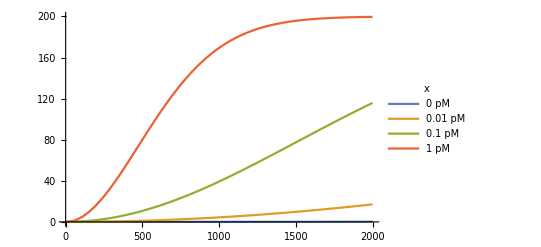

-Graphics-

-Graphics-

```mathematica
(*degRate =0*)
getProduct[viralLoad_, degRate_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial, cleavageRate} -> {viralLoad, degRate}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, cleavageRate],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-5, 10^-4 ,10^-3}}
resultTable=Evaluate@Table[getProduct[b,0],Evaluate@viralSweep]
p = Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000},PlotLegends->LineLegend[{"0 pM","0.01 pM", "0.1 pM", "1 pM"},LegendLabel->x], PlotRange->{0,200},FrameLabel->{Style["x axis",16,Bold],Style["y axis",16,Bold]}]
fts=FrameTicks/.AbsoluteOptions[p,FrameTicks];
fts[[1]]=ReplaceAll[#,{tick_,lbl_,{pos__},{style__}}:>{tick,If[lbl=="","",ToString[tick/(60)]~~"THz"],{pos},{style}}]&@fts[[1]];
p
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000},PlotLegends->LineLegend[{"0 pM","0.01 pM", "0.1 pM", "1 pM"},LegendLabel->x], PlotRange->{0,200},FrameTicks->fts,FrameLabel->{Style["x axis",16,Bold],Style["y axis",16,Bold]}]
```

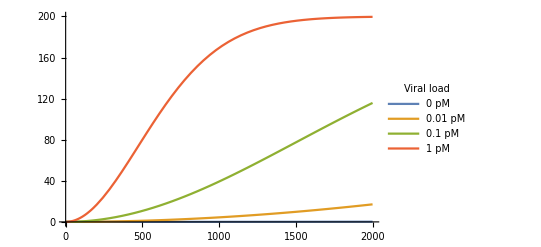

```mathematica
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000},PlotLegends->LineLegend[{"0 pM","0.01 pM", "0.1 pM", "1 pM"},LegendLabel->"Viral load"], PlotRange->{0,200},FrameLabel->{Style["x axis",22,Bold],Style["y axis",22,Bold]}]
```

-Graphics-

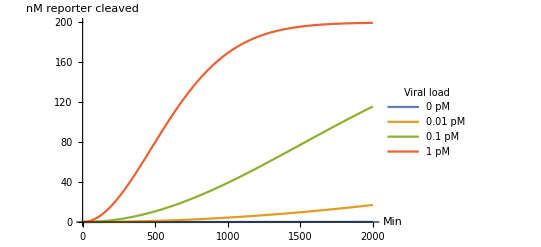

```mathematica
p = Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000},PlotLegends->LineLegend[{"0 pM","0.01 pM", "0.1 pM", "1 pM"},LegendLabel->"Viral load"], PlotRange->{0,200},TicksStyle->Large]
fts=FrameTicks/.AbsoluteOptions[p,FrameTicks];
fts[[1]]=ReplaceAll[#,{tick_,lbl_,{pos__},{style__}}:>{tick,If[lbl=="","",ToString[tick/(60)]~~"THz"],{pos},{style}}]&@fts[[1]];
Show[p,Ticks->{Charting`ScaledTicks[{60 #&,#/60&}],Automatic},AxesLabel->{"Min","nM reporter cleaved"}]
```

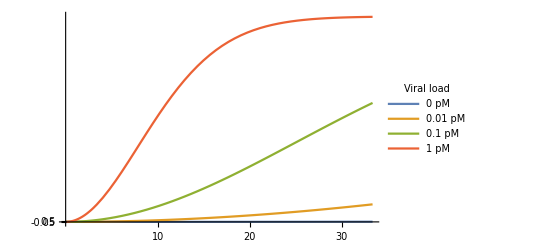

```mathematica
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000},PlotLegends->LineLegend[{"0 pM","0.01 pM", "0.1 pM", "1 pM"},LegendLabel->"Viral load"], PlotRange->{0,200},Ticks->{{{10*60,10,{.1,.05}},{20*60,20,{.1,.05}},{30*60,30,{.1,.05}}},{-0.05,0.5}},TicksStyle->Large]
```

```mathematica
p = Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000},PlotLegends->LineLegend[{"0 pM","0.01 pM", "0.1 pM", "1 pM"},LegendLabel->"Viral load"], PlotRange->{0,200},TicksStyle->Large]
fts=FrameTicks/.AbsoluteOptions[p,FrameTicks];
fts[[1]]=ReplaceAll[#,{tick_,lbl_,{pos__},{style__}}:>{tick,If[lbl=="","",ToString[tick/(60)]~~"THz"],{pos},{style}}]&@fts[[1]];
Show[p,Ticks->{Charting`ScaledTicks[{60 #&,#/60&},TicksLength->{.05,.02}],Charting`ScaledTicks[{Identity,Identity},TicksLength->{.05,.02}]},AxesStyle->Directive[Black,12],AxesLabel->{"Min","nM reporter cleaved"}]
```

-Graphics-

-Graphics-

{b,{0,1/100000,1/10000,1/1000}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

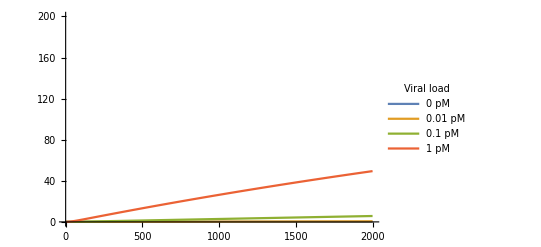

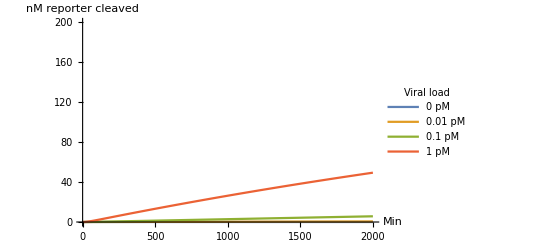

```mathematica
(*degRate =005*)
getProduct[viralLoad_, degRate_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial, cleavageRate} -> {viralLoad, degRate}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, cleavageRate],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-5, 10^-4 ,10^-3}}
resultTable=Evaluate@Table[getProduct[b,0.05],Evaluate@viralSweep]
p = Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000},PlotLegends->LineLegend[{"0 pM","0.01 pM", "0.1 pM", "1 pM"},LegendLabel->"Viral load"], PlotRange->{0,200},TicksStyle->Large]
fts=FrameTicks/.AbsoluteOptions[p,FrameTicks];
fts[[1]]=ReplaceAll[#,{tick_,lbl_,{pos__},{style__}}:>{tick,If[lbl=="","",ToString[tick/(60)]~~"THz"],{pos},{style}}]&@fts[[1]];
Show[p,Ticks->{Charting`ScaledTicks[{60 #&,#/60&},TicksLength->{.05,.02}],Charting`ScaledTicks[{Identity,Identity},TicksLength->{.05,.02}]},AxesStyle->Directive[Black,12],AxesLabel->{"Min","nM reporter cleaved"}]
```

```mathematica
Export["~/Documents/berkeley/SavageLab/scripts/covid_diagnostics_modeling/csm6_models/legend.svg",Show[p,Ticks->{Charting`ScaledTicks[{60 #&,#/60&}],Automatic},AxesLabel->{"Min","nM reporter cleaved"},ImageSize->{5 inch,5 inch}]]
Export["~/Documents/berkeley/SavageLab/scripts/covid_diagnostics_modeling/csm6_models/legend.png",Show[p,Ticks->{Charting`ScaledTicks[{60 #&,#/60&}],Automatic},AxesLabel->{"Min","nM reporter cleaved"},ImageSize->{5 inch,5 inch}]]
```

~/Documents/berkeley/SavageLab/scripts/covid_diagnostics_modeling/csm6_models/legend.svg

~/Documents/berkeley/SavageLab/scripts/covid_diagnostics_modeling/csm6_models/legend.png